## Constants

```mathematica
Zal=13;
Aal=27;
N0=6.02*10^23;
NeE137=1.86*10^20;
E0E137=20.;
fZ=αEMval^2 Zal^2(1/(1+αEMval^2 Zal^2)+0.20206-0.0369*αEMval^2 Zal^2+0.0083*αEMval^4 Zal^4-0.002*αEMval^6 Zal^6);
X0al=(ParamProductMass[11.]^2*Aal)/(4*αEMval^3*N0)*1/(Zal^2(Log[184.15*Zal^(-1/3)]-fZ)+Zal*Log[1194*Zal^(-2/3)])
```

9.35187×10^-27

## Flux of electrons

InterpolatingFunction::dmval: Input value {0.000919561} lies outside the range of data in the interpolating function. Extrapolation will be used.

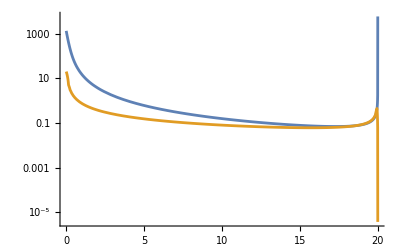

```mathematica
tmaxBreme=200;
Ie[E0_,Ee_,t_]= (*1/E0*(Log[E0/Ee])^(4/3 t-1)/Gamma[4/3 t]*)1/E0((E0-Ee)/E0)^(4/3 t-1)*4/3 t;
IeExact[E0_,Ee_,t_]=1/E0*(Log[E0/Ee])^(4/3 t-1)/Gamma[4/3 t];
fluxEapprox[E0_,Ee_]=-((Integrate[Ie[E0,Ee,t],t]/.{t->#})&/@{tmaxBreme,0})//Differences//First//Simplify;
If[!FileExistsQ[FileNameJoin[{NotebookDirectory[],"Bremsstrahlung data","Brem-e-data.mx"}]],
fluxEexact[Ee_]=Interpolation[Join[ParallelTable[{Ee,Quiet[NIntegrate[IeExact[E0E137,Ee,t],{t,0,tmaxBreme}]]},{Ee,0.05,E0E137-0.05,(E0E137-0.05-0.05)/200}],{{20.,Quiet[NIntegrate[IeExact[E0E137,E0E137,t],{t,0,tmaxBreme}]]}}],InterpolationOrder->1][Ee];
,
{fluxEexact[Ee_],γFluxInt[Ee_,mγ_]}=Import[FileNameJoin[{NotebookDirectory[],"Bremsstrahlung data","Brem-e-data.mx"}],"MX"];
]
LogPlot[Evaluate[{fluxEapprox[E0E137,Ee],fluxEexact[Ee]}],{Ee,ParamProductMass[11.],E0E137},PlotRange->All]
```

## Differential cross-section and number of events

### Effective photon flux (Eq. 3.4 from https://www-library.desy.de/preparch/desy/thesis/desy-thesis-13-024.pdf )

```mathematica
If[!FileExistsQ[FileNameJoin[{NotebookDirectory[],"Bremsstrahlung data","Brem-e-data.mx"}]],
ffRules = {a->(111*Zal^(-1/3))/ParamProductMass[11.], d-> 0.164*Aal^(-2/3),b->(773*Zal^(-2/3))/ParamProductMass[11.],μ->2.79};
G[t_]= (((a^2*t)/(1+a^2*t))^2*(1/(1+t/d))^2 Zal^2+((b^2*t)/(1+b^2*t))^2*((1+t/(4*ParamProductMass[2212.]^2)(μ^2-1))/(1+t/0.71)^4)^2 Zal)/. ffRules //Simplify;
γFluxIntegral[Ee_,mγ_]:=NIntegrate[G[t],{t,(mγ^2/(2Ee))^2,mγ^2}];
γFluxInt[Ee_,mγ_]=Interpolation[Flatten[ParallelTable[{Ee,mγ,γFluxIntegral[Ee,mγ]},{Ee,0.05,1.05*E0E137,0.1},{mγ,Join[{0.001,0.005,0.01,0.015},Table[m,{m,0.02,0.4,0.01}]]}],1],InterpolationOrder->1][Ee,mγ];
Export[FileNameJoin[{NotebookDirectory[],"Bremsstrahlung data","Brem-e-data.mx"}],{fluxEexact[Ee],γFluxInt[Ee,mγ]},"MX"]
]
```

### Differential number of produced LLPs

```mathematica
dσ[mγ_,ϵ2_,θγ_,Eγ_,Ee_,E0_]=θγ*8.*αEMval^3*ϵ2*Ee^2*xe*γFluxInt[Ee,mγ]*√(1-mγ^2/Ee^2)*((1-xe+xe^2/2)/U2+(1-xe)^2/U2^2 mγ^4-((1-xe)xe*mγ^2)/U2^(3/2))/.{U2->Ee^2*xe*θγ^2+mγ^2(1-xe)/xe+me^2 xe}/.{me->ParamProductMass[11.],xe->Eγ/Ee};
dNDP[mγ_,ϵ2_,θγ_,Eγ_,Ee_]=NeE137*(N0*X0al)/Aal*fluxEexact[Ee]*E0E137/Ee*dσ[mγ,ϵ2,θγ,Eγ,Ee,E0E137]//Simplify;
d2NDPdθγdEγ[mγ_,ϵ2_,θγ_,Eγ_]:=ϵ2*If[mγ<Eγ<E0E137&&θγ<=10^-2,NIntegrate[dNDP[mγ,1,θγ,Eγ,Ee],{Ee,Eγ+ParamProductMass[11.],E0E137}],0.]
NDP[mγ_,ϵ2_,θmax_,Emin_]:=NIntegrate[dNDP[mγ,1,θγ,Eγ,Ee],{θγ,0,θmax},{Eγ,Emin,E0E137-0.5},{Ee,Eγ+ParamProductMass[11.],E0E137},Method->(*"AdaptiveQuasiMonteCarlo"*)"AdaptiveMonteCarlo"]
(*MinMax[ParallelTable[NDP[0.1,1,0.03,2],50]]*)
```

#### Various LLP choices

```mathematica
d2PBremsstrahlungedθγdEγ["DP",mLLP_,ϵ2_,θLLP_,ELLP_]:=1/NeE137 d2NDPdθγdEγ[mLLP,ϵ2,θLLP,ELLP]
d2PBremsstrahlungedθγdEγ["B-L",mLLP_,αB_,θLLP_,ELLP_]:=1/NeE137 d2NDPdθγdEγ[mLLP,αB/αEMval,θLLP,ELLP]
d2PBremsstrahlungedθγdEγ["B-Le-3Lmu+Ltau",mLLP_,αB_,θLLP_,ELLP_]:=1/NeE137 d2NDPdθγdEγ[mLLP,αB/αEMval,θLLP,ELLP]
d2PBremsstrahlungedθγdEγ["B-3Le-Lmu+Ltau",mLLP_,αB_,θLLP_,ELLP_]:=1/NeE137 9*d2NDPdθγdEγ[mLLP,αB/αEMval,θLLP,ELLP]
```